```mathematica
yyy+1/x yy-2y=x^2;
x0=0.5;
yy0=-0.5;
y0=-1;
```

6

{0.5,0.6,0.7,0.8,0.9,1.}

{0.5,0.873021,1.2502,1.58193,1.8374,2.00885}

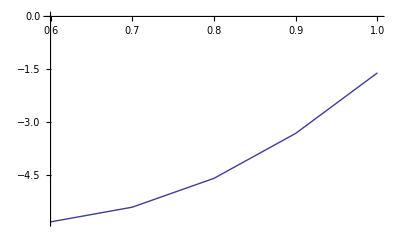

```mathematica
(*n=(b-a)/h+1;*)
f[x_,y_]:=-(x^2 y^2-(2x+1)y + 1)/x;
y0=0;


solve[f1_, f2_,f3_,y0_] :=(
a=0.5;
b=1;
h = 0.1;
X=Range[a,b,h];
n=Length[X];
Print[n];
Print[X];
Y=Table[{},{n}];
Y[[1]]=y0;
Z=Table[{},{n}];
Z[[1]]=z0;
For[i=2,i≤n,i++,
K1 = h f1[X[[i-1]],Y[[i-1]]];
K2 =  h f1[X[[i-1]] + h/2,Y[[i-1]] + K1/2];
K3 =  h f1[X[[i-1]] + h/2,Y[[i-1]] + K2/2];
K4 =  h f1[X[[i-1]] + h,Y[[i-1]] + K3];
delta = 1/6(K1 + 2 K2 + 2 K3 + K4);
Y[[i]]=Y[[i-1]]+delta;

K1 = h f2[X[[i-1]],Z[[i-1]],Y[[i]]];
K2 =  h f2[X[[i-1]] + h/2,Z[[i-1]] + K1/2,Y[[i]]];
K3 =  h f2[X[[i-1]] + h/2,Z[[i-1]] + K2/2,Y[[i]]];
K4 =  h f2[X[[i-1]] + h,Z[[i-1]] + K3,Y[[i]]];
delta2= 1/6(K1 + 2 K2 + 2 K3 + K4);
Z[[i]]=Z[[i-1]]+delta2;

];
Print[Y];
dots1=Table[{},{n}];
dots2=Table[{},{n}];
For[i=1,i≤n,i++,
dots1[[i]]={X[[i]],Y[[i]]};
dots2[[i]]={X[[i]],Z[[i]]};
];

(*ListLinePlot[dots]*)
Return[{dots1,dots2}];
);

f1[x_,y_]:=-y^2+  2/x y + 4/(x^2+2);(*y'*)
f2[x_,y_,a_]:=-y (a -2/x  ) +8;
f3[x_,y_,a_,b_] := (a y + b);
(*f3[x_,y_,z_]:=2/x z + 4/(x^2+2)y; *)
y0=0;
z0=0.5;
dots = solve[f1,f2,y0,z0];
dots11 = dots[[1]];
dots22 = dots[[2]];
T=Table[{},{6}];
T[[6]]=(1-dots22[[6,2]])/(1+dots11[[6,2]]);
For[i=5,i≥2,i--,
K1 = h f3[X[[i+1]],Z[[i+1]],Y[[i]],Z[[i]]];
K2 =  h f3[X[[i+1]] + h/2,Z[[i+1]] + K1/2,Y[[i]],Z[[i]]];
K3 =  h f3[X[[i+1]] + h/2,Z[[i+1]] + K2/2,Y[[i]],Z[[i]]];
K4 =  h f3[X[[i+1]] + h,Z[[i+1]] + K3,Y[[i]],Z[[i]]];
delta3= 1/6(K1 + 2 K2 + 2 K3 + K4);
T[[i]]=T[[i+1]]-delta3;
];
dots=Table[{},{n}];
For[i=1,i≤n,i++,
dots[[i]]={X[[i]],T[[i]]};
];
ListLinePlot[dots]
```